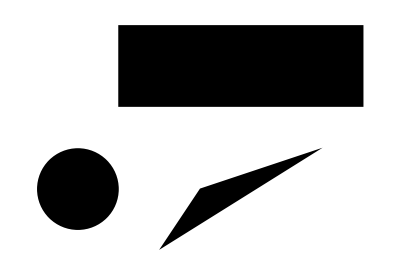

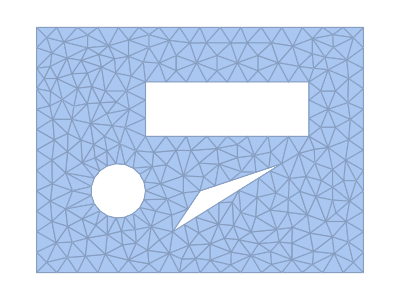

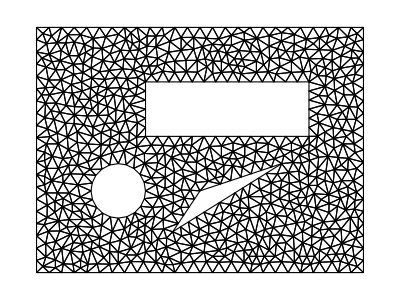

NDSolveValue::bcnop: No places were found on the boundary where {x,y}∈Circle[{0,0}] was True, so DirichletCondition[u==3,{x,y}∈Circle[{0,0}]] will effectively be ignored.

NDSolveValue::bcnop: No places were found on the boundary where {x,y}∈Line[{{1,2},{7,2},{7,4},{1,4},{1,2}}] was True, so DirichletCondition[u==2,{x,y}∈Line[{{1,2},{7,2},{7,4},{1,4},{1,2}}]] will effectively be ignored.

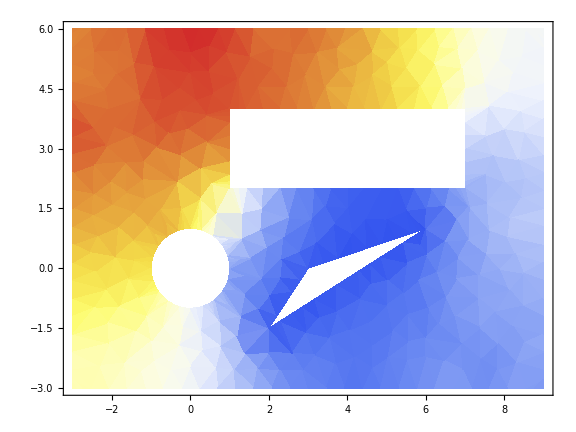

```mathematica
Clear["Global`*"]
Needs["NDSolve`FEM`"]
Ω={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};
rect=Rectangle[{-3,-3},{9,6}];

Graphics[Ω]

DiscretizeRegion[RegionDifference[Rectangle[{-3,-3},{9,6}],RegionUnion@@Ω]]
mesh=ToElementMesh[RegionDifference[rect,RegionUnion@@Ω],MaxCellMeasure->0.1];
mesh["Wireframe"]

op=-Laplacian[u[x,y],{x,y}];

Γ1=DirichletCondition[u[x,y]==3, {x,y}∈RegionBoundary[Disk[]]];
Γ2=DirichletCondition[u[x,y]==2, {x,y}∈RegionBoundary[Rectangle[{1,2},{7,4}]]];
Γ3=DirichletCondition[u[x,y]==1, {x,y}∈RegionBoundary[Triangle[{{3,0},{6,1},{2,-1.5}}]]];

sol=NDSolveValue[{op==0,Γ1,Γ2,Γ3},u[x,y],{x,y}∈mesh];
Show[
DensityPlot[sol,{x,y}∈mesh,AspectRatio->Automatic,ImageSize->Large,ColorFunction->"TemperatureMap"]]
```